```mathematica
Tanh[Log[1-t^2]]
```

(-1+(1-t^2)^2)/(1+(1-t^2)^2)

```mathematica
S[t_]:=Tanh[Log[1-t^2]]
```

```mathematica
FullSimplify[Abs[S'[t]]]
```

8 Abs[(t (-1+t^2))/((2-2 t^2+t^4)^2)]

```mathematica
Sd[t_]:=8 Abs[(t (-1+t^2))/((2-2 t^2+t^4)^2)]
```

```mathematica
Map[Simplify,Solve[S[t]==y,t]]
```

{{t→-√((-1+y-√(1-y^2))/(-1+y))},{t→√((-1+y-√(1-y^2))/(-1+y))},{t→-√((-1+y+√(1-y^2))/(-1+y))},{t→√((-1+y+√(1-y^2))/(-1+y))}}

```mathematica
Transfer[f_]:=(f[-√((-1+y-√(1-y^2))/(-1+y))]+f[√((-1+y-√(1-y^2))/(-1+y))])/(2 Abs[√(-1+y) √(1-y^2) √(1-y+√(1-y^2))])+(f[-√((-1+y+√(1-y^2))/(-1+y))]+f[√((-1+y+√(1-y^2))/(-1+y))])/(2 Abs[√(-1+y) √(1-y^2) √(-1+y+√(1-y^2))])
```

```mathematica
Sin[-√((-1+y-√(1-y^2))/(-1+y))]+Sin[√((-1+y-√(1-y^2))/(-1+y))]
```

```mathematica
S[Sqrt[2]]
```

0

```mathematica
Solve[1/S[t]==0]
```

{{t→-√(1-ⅈ)},{t→√(1-ⅈ)},{t→-√(1+ⅈ)},{t→√(1+ⅈ)}}

```mathematica
Solve[FullSimplify[t-S[t]/S'[t]]==y,t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
Solve[-S[t]/S'[t]==y,t]
```

{{t→Root[-8 y-4 #1+8 y #1^2+6 #1^3-4 #1^5+#1^7&,1]},{t→Root[-8 y-4 #1+8 y #1^2+6 #1^3-4 #1^5+#1^7&,2]},{t→Root[-8 y-4 #1+8 y #1^2+6 #1^3-4 #1^5+#1^7&,3]},{t→Root[-8 y-4 #1+8 y #1^2+6 #1^3-4 #1^5+#1^7&,4]},{t→Root[-8 y-4 #1+8 y #1^2+6 #1^3-4 #1^5+#1^7&,5]},{t→Root[-8 y-4 #1+8 y #1^2+6 #1^3-4 #1^5+#1^7&,6]},{t→Root[-8 y-4 #1+8 y #1^2+6 #1^3-4 #1^5+#1^7&,7]}}

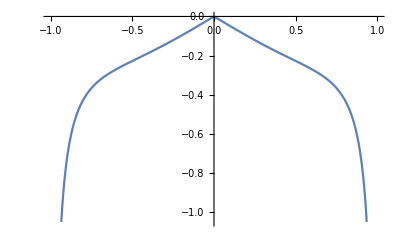

```mathematica
Plot[S[t]/Abs[S'[t]],{t,-1,1}]
```

```mathematica
S[t]
```

S[t]

```mathematica
Transfer[Sin]
```

0

```mathematica
In[5]:=√((-1+y-√(1-y^2))/(-1+y))-√((-1+y-√(1-y^2))/(-1+y))
```

0

```mathematica
?Identity
```

```mathematica
FullSimplify[Sd[-√((-1+y-√(1-y^2))/(-1+y))]]
```

Sd[-√(1+(1+y)/(√(1-y^2)))]

```mathematica
FullSimplify[Sd[√((-1+y-√(1-y^2))/(-1+y))]]
```

2 Abs[√(-1+y) √(1-y^2) √(1-y+√(1-y^2))]

```mathematica
FullSimplify[Sd[-√((-1+y+√(1-y^2))/(-1+y))]]
```

2 Abs[√(-1+y) √(1-y^2) √(-1+y+√(1-y^2))]

```mathematica
FullSimplify[Sd[√((-1+y+√(1-y^2))/(-1+y))]]
```

2 Abs[√(-1+y) √(1-y^2) √(-1+y+√(1-y^2))]

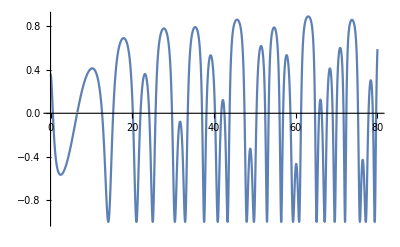

```mathematica
Plot[S[t],{t,0,80}]
```

```mathematica
Solve[S[t]==0,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→S^(-1)[0]}}

```mathematica
ContourPlot[{Re[S[x+I*y]]==-1,Re[S[x+I*y]]==0,Re[S[x+I*y]]==1,Im[S[x+I*y]]==1,Im[S[x+I*y]]==-1,Im[S[x+I*y]]==0},{x,10,40},{y,-5,5},PerformanceGoal->"HighQuality",MaxRecursion->5]
```

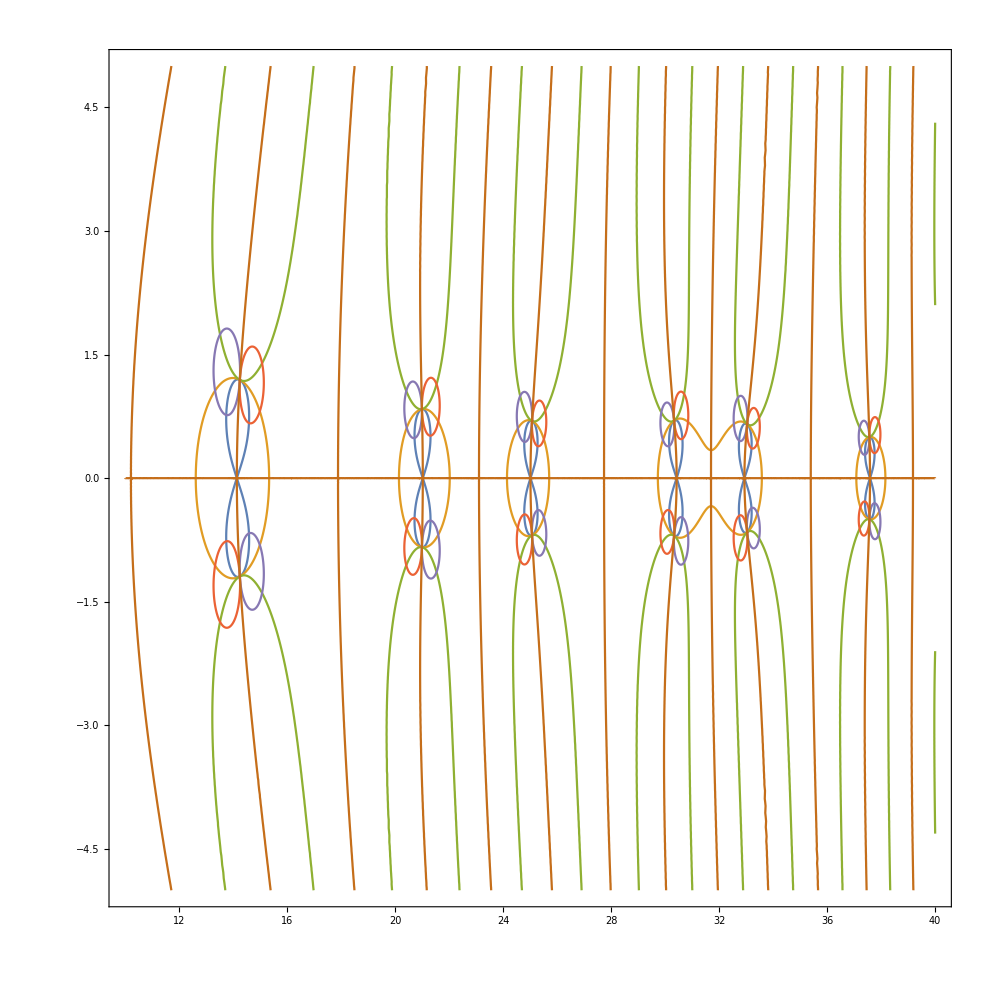
```mathematica
-Graphics-8 Abs[(t (-1+t^2))/((2-2 t^2+t^4)^2)]
```

```mathematica
·
```

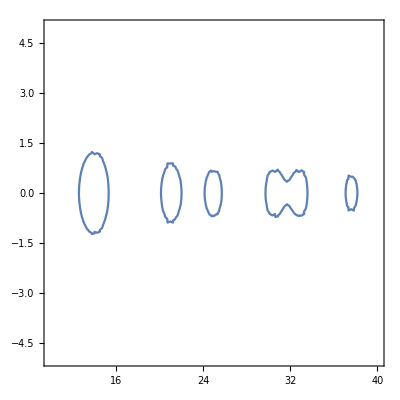

```mathematica
ContourPlot[{},{x,10,40},{y,-5,5},PerformanceGoal->"HighQuality"]
```

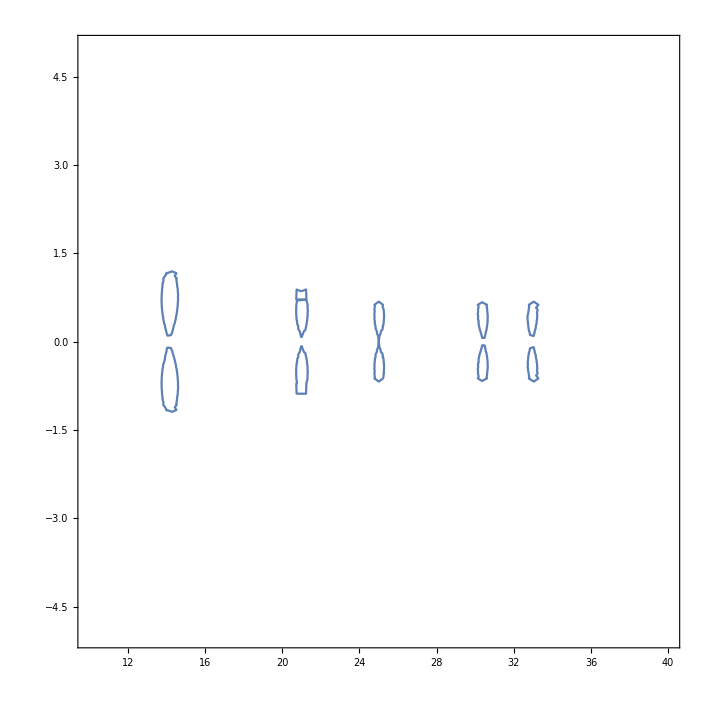

```mathematica
ContourPlot
```

```mathematica
ContourPlot[Re[S[x+I*y]]==0,{x,-2,2},{y,-2,2},PerformanceGoal->"Quality"]
```

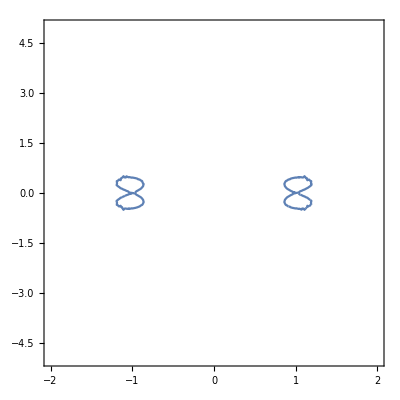
```mathematica
-Graphics--Graphics-
```